# Método de los momentos dividiendo el dominio - Normal estándar

```mathematica
(*Muestra de la distribución Normal(0,1)*)
```

```mathematica
SeedRandom[1234]
```

```mathematica
data1= RandomVariate[NormalDistribution[0,1],10001]
```

{-0.508336,-0.0706019,-1.5939,1.53659,2.67802,-1.31683,-1.09456,0.142948,0.104166,-1.67311,0.0357514,0.170186,0.934682,-0.826864,9973,0.622688,-0.538344,1.10496,-0.342243,1.0691,-0.852105,0.249137,1.09009,0.0543596,-1.12438,-1.15048,0.35102,0.954185,-0.387142}
 |  |  |  |

```mathematica
data=Delete[data1,7615]
```

{-0.508336,-0.0706019,-1.5939,1.53659,2.67802,-1.31683,-1.09456,0.142948,0.104166,-1.67311,0.0357514,0.170186,0.934682,-0.826864,9972,0.622688,-0.538344,1.10496,-0.342243,1.0691,-0.852105,0.249137,1.09009,0.0543596,-1.12438,-1.15048,0.35102,0.954185,-0.387142}
 |  |  |  |

### MOP DE GRADO 3

```mathematica
F3[x_] = Piecewise[{{a+b*x+c*x^2+d*x^3,-Infinity<x<0},{e+f*x+g*x^2+h*x^3,0≤x<Infinity}},0]
```

Piecewise[{{a+b x+c x^2+d x^3, -∞<x<0}, {e+f x+g x^2+h x^3, 0≤x<∞}, {0, True}}]

```mathematica
(*Momentos poblacionales*)
```

```mathematica
Integrate[x*F3[x],{x,-4,4}]
```

-8/15 (15 a-40 b+120 c-384 d-15 e-40 f-120 g-384 h)

```mathematica
Integrate[x^2*F3[x],{x,-4,4}]
```

64/15 (5 a-15 b+48 c-160 d+5 e+15 f+48 g+160 h)

```mathematica
Integrate[x^3*F3[x],{x,-4,4}]
```

-64/105 (105 a-336 b+1120 c-3840 d-105 e-336 f-1120 g-3840 h)

```mathematica
Integrate[x^4*F3[x],{x,-4,4}]
```

1024/105 (21 a-70 b+240 c-840 d+21 e+70 f+240 g+840 h)

```mathematica
Integrate[x^5*F3[x],{x,-4,4}]
```

-2048/63 (21 a-72 b+252 c-896 d-21 e-72 f-252 g-896 h)

```mathematica
Integrate[x^6*F3[x],{x,-4,4}]
```

8192/315 (90 a-315 b+1120 c-4032 d+90 e+315 f+1120 g+4032 h)

```mathematica
Integrate[x^7*F3[x],{x,-4,4}]
```

-8192/495 (495 a-1760 b+6336 c-23040 d-495 e-1760 f-6336 g-23040 h)

```mathematica
Integrate[x^8*F3[x],{x,-4,4}]
```

262144/495 (55 a-198 b+720 c-2640 d+55 e+198 f+720 g+2640 h)

```mathematica
(*Solución del sistema*)
```

```mathematica
Solve[{-8/15 (15 a-40 b+120 c-384 d-15 e-40 f-120 g-384 h)==(Apply[Plus,data])/(10^4),64/15 (5 a-15 b+48 c-160 d+5 e+15 f+48 g+160 h)==(Apply[Plus,data^2])/(10^4),-64/105 (105 a-336 b+1120 c-3840 d-105 e-336 f-1120 g-3840 h)==(Apply[Plus,data^3])/(10^4),1024/105 (21 a-70 b+240 c-840 d+21 e+70 f+240 g+840 h)==(Apply[Plus,data^4])/(10^4),-2048/63 (21 a-72 b+252 c-896 d-21 e-72 f-252 g-896 h)==(Apply[Plus,data^5])/(10^4),8192/315 (90 a-315 b+1120 c-4032 d+90 e+315 f+1120 g+4032 h)==(Apply[Plus,data^6])/(10^4),-8192/495 (495 a-1760 b+6336 c-23040 d-495 e-1760 f-6336 g-23040 h)==(Apply[Plus,data^7])/(10^4),262144/495 (55 a-198 b+720 c-2640 d+55 e+198 f+720 g+2640 h)==(Apply[Plus,data^8])/(10^4)},{a,b,c,d,e,f,g,h}]
```

{{a→0.627694,b→0.524182,c→0.146622,d→0.0137127,e→0.592475,f→-0.486502,g→0.132842,h→-0.0120515}}

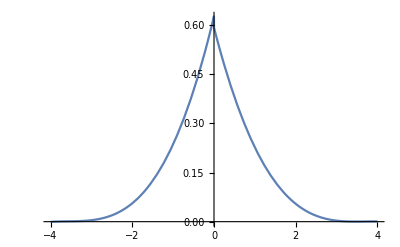

```mathematica
Plot[F3[x]/.{a->0.6276944587506358,b->0.524182371172012,c->0.14662232829264832,d->0.013712667558948207,e->0.5924752772356712,f->-0.4865017071851931,g->0.13284158040682476,h->-0.01205151291873122},{x,-4,4}]
```

```mathematica
(*Obtención de la función de densidad y representación gráfica*)
```

```mathematica
Solve[F3[x]==0/.{a->0.6276944587506358,b->0.524182371172012,c->0.14662232829264832,d->0.013712667558948207,e->0.5924752772356712,f->-0.4865017071851931,g->0.13284158040682476,h->-0.01205151291873122},Reals]
```

{{x→-3.91355},{x→4.14924}}

```mathematica
F31[x_]=F3[x]/.{a->0.6276944587506358,b->0.524182371172012,c->0.14662232829264832,d->0.013712667558948207,e->0.5924752772356712,f->-0.4865017071851931,g->0.13284158040682476,h->-0.01205151291873122}
```

Piecewise[{{0.627694+0.524182 x+0.146622 x^2+0.0137127 x^3, -∞≤x<0}, {0.592475-0.486502 x+0.132842 x^2-0.0120515 x^3, 0≤x≤∞}, {0, True}}]

```mathematica
F31[4]
```

0.000636908

```mathematica
F31[-3.9135518663581763]
```

-2.22045×10^-16

```mathematica
F31[-4]
```

-0.000688497

```mathematica
F32[x_]=  Piecewise[{{0.6276944587506358+0.524182371172012 x+0.14662232829264832 x^2+0.013712667558948207 x^3+0.000688497027724555,-Infinity≤x<0},{0.5924752772356712-0.4865017071851931 x+0.13284158040682476 x^2-0.01205151291873122 x^3,0≤x≤Infinity}},0]
```

Piecewise[{{0.628383+0.524182 x+0.146622 x^2+0.0137127 x^3, -∞≤x<0}, {0.592475-0.486502 x+0.132842 x^2-0.0120515 x^3, 0≤x≤∞}, {0, True}}]

```mathematica
Integrate[F32[x],{x,-4,4}]
```

1.11095

```mathematica
f3[x_]= Piecewise[{{(0.6283829557783603+0.524182371172012 x+0.14662232829264832 x^2+0.013712667558948207 x^3)/1.1109494735490946,-Infinity<x<0},{(0.5924752772356712-0.4865017071851931 x+0.13284158040682476 x^2-0.01205151291873122 x^3)/1.1109494735490946,0≤x<Infinity}},0]
```

Piecewise[{{0.900131 (0.628383+0.524182 x+0.146622 x^2+0.0137127 x^3), -∞<x<0}, {0.900131 (0.592475-0.486502 x+0.132842 x^2-0.0120515 x^3), 0≤x<∞}, {0, True}}]

```mathematica
Integrate[f3[x],{x,-4,4}]
```

1.

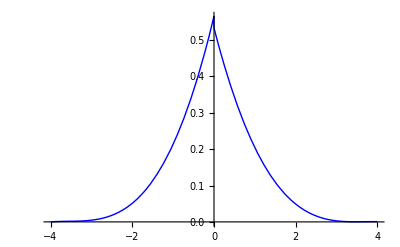

```mathematica
Plot[f3[x],{x,-4,4},PlotStyle->{Blue,Thin}]
```

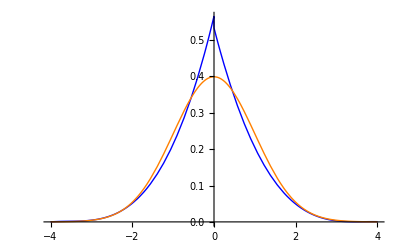

```mathematica
Plot[{f3[x],PDF[NormalDistribution[0,1],x]},{x,-4,4},PlotStyle->{{Blue,Thin},{Orange,Thin}}]
```

```mathematica
(*Divergencia de Kullback-Leibler*)
```

```mathematica
N[Integrate[PDF[NormalDistribution[0,1],x],{x,-4,4}]]
```

0.999937

```mathematica
F[x_]=(PDF[NormalDistribution[0,1],x])/0.9999366575163338
```

0.398968 ⅇ^(-x^2/2)

```mathematica
KL3 = N[Integrate[F[x]*Log[F[x]/f3[x]],{x,-4,4}]]
```

0.0115246

```mathematica
(*Verosimilitud*)
```

```mathematica
x3=Log[Table[f3[Extract[data,i]],{i,1,10000}]]
```

{-1.0265,-0.629294,-2.31378,-2.26934,-4.62767,-1.93119,-1.65491,-0.74841,-0.715444,-2.43226,-0.658163,-0.771783,-1.51595,-1.35192,9972,-1.18953,-1.05572,-1.71045,-0.869623,-1.66841,-1.37925,-0.840584,-1.69294,-0.673635,-1.69057,-1.72213,-0.931779,-1.53759,-0.91124}
 |  |  |  |

```mathematica
V3=Apply[Plus,x3]
```

-14248.

```mathematica
(*BIC*)
```

```mathematica
BIC3 = -2*V3 + 8*Log[10000]
```

28569.7

```mathematica
F4[x_] = Piecewise[{{a+b*x+c*x^2+d*x^3+e*x^4,-Infinity<x<0},{f+g*x+h*x^2+i*x^3+j*x^4,0≤x<Infinity}},0]
```

Piecewise[{{a+b x+c x^2+d x^3+e x^4, -∞<x<0}, {f+g x+h x^2+i x^3+j x^4, 0≤x<∞}, {0, True}}]

```mathematica
(*Momentos poblacionales*)
```

```mathematica
Integrate[x*F4[x],{x,-4,4}]
```

-8/15 (15 a-40 b+120 c-384 d+1280 e-15 f-40 g-120 h-384 i-1280 j)

```mathematica
Integrate[x^2*F4[x],{x,-4,4}]
```

64/105 (35 a-105 b+336 c-1120 d+3840 e+35 f+105 g+336 h+1120 i+3840 j)

```mathematica
Integrate[x^3*F4[x],{x,-4,4}]
```

-64/105 (105 a-336 b+1120 c-3840 d+13440 e-105 f-336 g-1120 h-3840 i-13440 j)

```mathematica
Integrate[x^4*F4[x],{x,-4,4}]
```

1024/315 (63 a-210 b+720 c-2520 d+8960 e+63 f+210 g+720 h+2520 i+8960 j)

```mathematica
Integrate[x^5*F4[x],{x,-4,4}]
```

-2048/315 (105 a-360 b+1260 c-4480 d+16128 e-105 f-360 g-1260 h-4480 i-16128 j)

```mathematica
Integrate[x^6*F4[x],{x,-4,4}]
```

(8192 (990 a-3465 b+12320 c-44352 d+161280 e+990 f+3465 g+12320 h+44352 i+161280 j))/3465

```mathematica
Integrate[x^7*F4[x],{x,-4,4}]
```

-8192/495 (495 a-1760 b+6336 c-23040 d+84480 e-495 f-1760 g-6336 h-23040 i-84480 j)

```mathematica
Integrate[x^8*F4[x],{x,-4,4}]
```

(262144 (715 a-2574 b+9360 c-34320 d+126720 e+715 f+2574 g+9360 h+34320 i+126720 j))/6435

```mathematica
Integrate[x^9*F4[x],{x,-4,4}]
```

-(524288 (3003 a-10920 b+40040 c-147840 d+549120 e-3003 f-10920 g-40040 h-147840 i-549120 j))/15015

```mathematica
Integrate[x^10*F4[x],{x,-4,4}]
```

(4194304 (1365 a-5005 b+18480 c-68640 d+256256 e+1365 f+5005 g+18480 h+68640 i+256256 j))/15015

```mathematica
(*Solución del sistema*)
```

```mathematica
Solve[{-8/15 (15 a-40 b+120 c-384 d+1280 e-15 f-40 g-120 h-384 i-1280 j)==(Apply[Plus,data])/(10^4),64/105 (35 a-105 b+336 c-1120 d+3840 e+35 f+105 g+336 h+1120 i+3840 j)==(Apply[Plus,data^2])/(10^4),-64/105 (105 a-336 b+1120 c-3840 d+13440 e-105 f-336 g-1120 h-3840 i-13440 j)==(Apply[Plus,data^3])/(10^4),1024/315 (63 a-210 b+720 c-2520 d+8960 e+63 f+210 g+720 h+2520 i+8960 j)==(Apply[Plus,data^4])/(10^4),-2048/315 (105 a-360 b+1260 c-4480 d+16128 e-105 f-360 g-1260 h-4480 i-16128 j)==(Apply[Plus,data^5])/(10^4),(8192 (990 a-3465 b+12320 c-44352 d+161280 e+990 f+3465 g+12320 h+44352 i+161280 j))/3465==(Apply[Plus,data^6])/(10^4),-8192/495 (495 a-1760 b+6336 c-23040 d+84480 e-495 f-1760 g-6336 h-23040 i-84480 j)==(Apply[Plus,data^7])/(10^4),(262144 (715 a-2574 b+9360 c-34320 d+126720 e+715 f+2574 g+9360 h+34320 i+126720 j))/6435==(Apply[Plus,data^8])/(10^4),-(524288 (3003 a-10920 b+40040 c-147840 d+549120 e-3003 f-10920 g-40040 h-147840 i-549120 j))/15015==(Apply[Plus,data^9])/(10^4),(4194304 (1365 a-5005 b+18480 c-68640 d+256256 e+1365 f+5005 g+18480 h+68640 i+256256 j))/15015==(Apply[Plus,data^10])/(10^4)},{a,b,c,d,e,f,g,h,i,j}]
```

{{a→0.608517,b→0.485661,c→0.120769,d→0.00659556,e→-0.000692156,f→0.571237,g→-0.442909,h→0.103124,i→-0.00377225,j→-0.0008129}}

```mathematica
(*Obtención de la función de densidad y representación gráfica*)
```

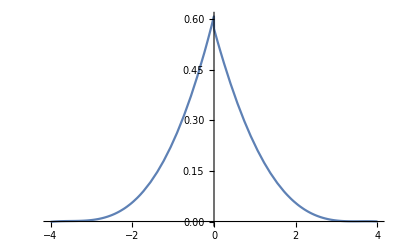

```mathematica
Plot[F4[x]/.{a->0.6085170709427672,b->0.4856610069706638,c->0.12076859499536975,d->0.006595562881642501,e->-0.0006921556683866477,f->0.5712371897512089,g->-0.4429090898695681,h->0.10312403521703048,i->-0.0037722460520208125,j->-0.0008128997926738096},{x,-4,4}]
```

```mathematica
Solve[F4[x]==0/.{a->0.6085170709427672,b->0.4856610069706638,c->0.12076859499536975,d->0.006595562881642501,e->-0.0006921556683866477,f->0.5712371897512089,g->-0.4429090898695681,h->0.10312403521703048,i->-0.0037722460520208125,j->-0.0008128997926738096},Reals]
```

{{x→-3.89557},{x→4.00818}}

```mathematica
F41[x_]=F4[x]/.{a->0.6085170709427672,b->0.4856610069706638,c->0.12076859499536975,d->0.006595562881642501,e->-0.0006921556683866477,f->0.5712371897512089,g->-0.4429090898695681,h->0.10312403521703048,i->-0.0037722460520208125,j->-0.0008128997926738096}
```

Piecewise[{{0.608517+0.485661 x+0.120769 x^2+0.00659556 x^3-0.000692156 x^4, -∞<x<0}, {0.571237-0.442909 x+0.103124 x^2-0.00377225 x^3-0.0008129 x^4, 0≤x<∞}, {0, True}}]

```mathematica
F41[-4]
```

-0.00113731

```mathematica
F42[x_]=Piecewise[{{0.6085170709427672+0.4856610069706638 x+0.12076859499536975 x^2+0.006595562881642501 x^3-0.0006921556683866477 x^4+0.0011373125460738542,-Infinity<x<0},{0.5712371897512089-0.4429090898695681 x+0.10312403521703048 x^2-0.0037722460520208125 x^3-0.0008128997926738096 x^4,0≤x<Infinity}},0]
```

Piecewise[{{0.609654+0.485661 x+0.120769 x^2+0.00659556 x^3-0.000692156 x^4, -∞<x<0}, {0.571237-0.442909 x+0.103124 x^2-0.00377225 x^3-0.0008129 x^4, 0≤x<∞}, {0, True}}]

```mathematica
Integrate[F42[x],{x,-4,4}]
```

1.09961

```mathematica
f4[x_]=Piecewise[{{(0.609654383488841+0.4856610069706638 x+0.12076859499536975 x^2+0.006595562881642501 x^3-0.0006921556683866477 x^4)/1.0996064992565824,-Infinity<x<0},{(0.5712371897512089-0.4429090898695681 x+0.10312403521703048 x^2-0.0037722460520208125 x^3-0.0008128997926738096 x^4)/1.0996064992565824,0≤x<Infinity}},0]
```

Piecewise[{{0.909416 (0.609654+0.485661 x+0.120769 x^2+0.00659556 x^3-0.000692156 x^4), -∞<x<0}, {0.909416 (0.571237-0.442909 x+0.103124 x^2-0.00377225 x^3-0.0008129 x^4), 0≤x<∞}, {0, True}}]

```mathematica
Integrate[f4[x],{x,-4,4}]
```

1.

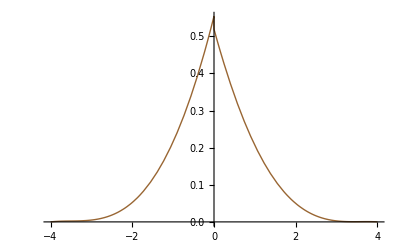

```mathematica
Plot[f4[x],{x,-4,4},PlotStyle->{Brown,Thin}]
```

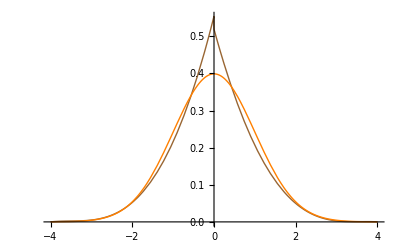

```mathematica
Plot[{f4[x],PDF[NormalDistribution[0,1],x]},{x,-4,4},PlotStyle->{{Brown,Thin},{Orange,Thin}}]
```

```mathematica
(*Divergencia de Kullback-Leibler*)
```

```mathematica
N[Integrate[PDF[NormalDistribution[0,1],x],{x,-4,4}]]
```

0.999937

```mathematica
F[x_]=(PDF[NormalDistribution[0,1],x])/0.9999366575163338
```

0.398968 ⅇ^(-x^2/2)

```mathematica
KL4 = N[Integrate[F[x]*Log[F[x]/f4[x]],{x,-4,4}]]
```

0.00995931

```mathematica
(*Verosimilitud*)
```

```mathematica
x4=Log[Table[f4[Extract[data,i]],{i,1,10000}]]
```

{-1.02872,-0.64666,-2.29138,-2.24967,-4.65705,-1.91266,-1.64088,-0.768257,-0.736996,-2.40917,-0.682778,-0.790447,-1.50698,-1.34463,9972,-1.19038,-1.05699,-1.69718,-0.877342,-1.65598,-1.37127,-0.855883,-1.68002,-0.697409,-1.67588,-1.70687,-0.942888,-1.52809,-0.917441}
 |  |  |  |

```mathematica
V4=Apply[Plus,x4]
```

-14234.1

```mathematica
(*BIC*)
```

```mathematica
BIC4 = -2*V4 + 10*Log[10000]
```

28560.3

### MOP DE GRADO 5

```mathematica
F5[x_] = Piecewise[{{a+b*x+c*x^2+d*x^3+e*x^4+f*x^5,-Infinity<x<0},{g+h*x+i*x^2+j*x^3+k*x^4+l*x^5,0≤x<Infinity}},0]
```

Piecewise[{{a+b x+c x^2+d x^3+e x^4+f x^5, -∞<x<0}, {g+h x+i x^2+j x^3+k x^4+l x^5, 0≤x<∞}, {0, True}}]

```mathematica
(*Momentos poblacionales*)
```

```mathematica
Integrate[x*F5[x],{x,-4,4}]
```

-8/105 (105 a-280 b+840 c-2688 d+8960 e-30720 f-105 g-280 h-840 i-2688 j-8960 k-30720 l)

```mathematica
Integrate[x^2*F5[x],{x,-4,4}]
```

64/105 (35 a-105 b+336 c-1120 d+3840 e-13440 f+35 g+105 h+336 i+1120 j+3840 k+13440 l)

```mathematica
Integrate[x^3*F5[x],{x,-4,4}]
```

-64/315 (315 a-1008 b+3360 c-11520 d+40320 e-143360 f-315 g-1008 h-3360 i-11520 j-40320 k-143360 l)

```mathematica
Integrate[x^4*F5[x],{x,-4,4}]
```

1024/315 (63 a-210 b+720 c-2520 d+8960 e-32256 f+63 g+210 h+720 i+2520 j+8960 k+32256 l)

```mathematica
Integrate[x^5*F5[x],{x,-4,4}]
```

-1/3465 2048 (1155 a-3960 b+13860 c-49280 d+177408 e-645120 f-1155 g-3960 h-13860 i-49280 j-177408 k-645120 l)

```mathematica
Integrate[x^6*F5[x],{x,-4,4}]
```

1/3465 8192 (990 a-3465 b+12320 c-44352 d+161280 e-591360 f+990 g+3465 h+12320 i+44352 j+161280 k+591360 l)

```mathematica
Integrate[x^7*F5[x],{x,-4,4}]
```

-1/6435 8192 (6435 a-22880 b+82368 c-299520 d+1098240 e-4055040 f-6435 g-22880 h-82368 i-299520 j-1098240 k-4055040 l)

```mathematica
Integrate[x^8*F5[x],{x,-4,4}]
```

1/45045 262144 (5005 a-18018 b+65520 c-240240 d+887040 e-3294720 f+5005 g+18018 h+65520 i+240240 j+887040 k+3294720 l)

```mathematica
Integrate[x^9*F5[x],{x,-4,4}]
```

-1/15015 524288 (3003 a-10920 b+40040 c-147840 d+549120 e-2050048 f-3003 g-10920 h-40040 i-147840 j-549120 k-2050048 l)

```mathematica
Integrate[x^10*F5[x],{x,-4,4}]
```

1/15015 4194304 (1365 a-5005 b+18480 c-68640 d+256256 e-960960 f+1365 g+5005 h+18480 i+68640 j+256256 k+960960 l)

```mathematica
Integrate[x^11*F5[x],{x,-4,4}]
```

-(4194304 (7735 a-28560 b+106080 c-396032 d+1485120 e-5591040 f-7735 g-28560 h-106080 i-396032 j-1485120 k-5591040 l))/23205

```mathematica
Integrate[x^12*F5[x],{x,-4,4}]
```

(67108864 (5355 a-19890 b+74256 c-278460 d+1048320 e-3960320 f+5355 g+19890 h+74256 i+278460 j+1048320 k+3960320 l))/69615

```mathematica
(*Solución del sistema*)
```

```mathematica
Solve[{-8/105 (105 a-280 b+840 c-2688 d+8960 e-30720 f-105 g-280 h-840 i-2688 j-8960 k-30720 l)==(Apply[Plus,data])/(10^4),64/105 (35 a-105 b+336 c-1120 d+3840 e-13440 f+35 g+105 h+336 i+1120 j+3840 k+13440 l)==(Apply[Plus,data^2])/(10^4),-64/315 (315 a-1008 b+3360 c-11520 d+40320 e-143360 f-315 g-1008 h-3360 i-11520 j-40320 k-143360 l)==(Apply[Plus,data^3])/(10^4),1024/315 (63 a-210 b+720 c-2520 d+8960 e-32256 f+63 g+210 h+720 i+2520 j+8960 k+32256 l)==(Apply[Plus,data^4])/(10^4),-1/3465 2048 (1155 a-3960 b+13860 c-49280 d+177408 e-645120 f-1155 g-3960 h-13860 i-49280 j-177408 k-645120 l)==(Apply[Plus,data^5])/(10^4),1/3465 8192 (990 a-3465 b+12320 c-44352 d+161280 e-591360 f+990 g+3465 h+12320 i+44352 j+161280 k+591360 l)==(Apply[Plus,data^6])/(10^4),-1/6435 8192 (6435 a-22880 b+82368 c-299520 d+1098240 e-4055040 f-6435 g-22880 h-82368 i-299520 j-1098240 k-4055040 l)==(Apply[Plus,data^7])/(10^4),1/45045 262144 (5005 a-18018 b+65520 c-240240 d+887040 e-3294720 f+5005 g+18018 h+65520 i+240240 j+887040 k+3294720 l)==(Apply[Plus,data^8])/(10^4),-1/15015 524288 (3003 a-10920 b+40040 c-147840 d+549120 e-2050048 f-3003 g-10920 h-40040 i-147840 j-549120 k-2050048 l)==(Apply[Plus,data^9])/(10^4),1/15015 4194304 (1365 a-5005 b+18480 c-68640 d+256256 e-960960 f+1365 g+5005 h+18480 i+68640 j+256256 k+960960 l)==(Apply[Plus,data^10])/(10^4),-1/23205 4194304 (7735 a-28560 b+106080 c-396032 d+1485120 e-5591040 f-7735 g-28560 h-106080 i-396032 j-1485120 k-5591040 l)==(Apply[Plus,data^11])/(10^4),1/69615 67108864 (5355 a-19890 b+74256 c-278460 d+1048320 e-3960320 f+5355 g+19890 h+74256 i+278460 j+1048320 k+3960320 l)==(Apply[Plus,data^12])/(10^4)},{a,b,c,d,e,f,g,h,i,j,k,l}]
```

{{a→0.465829,b→0.071478,c→-0.297709,d→-0.185448,e→-0.0417262,f→-0.00331814,g→0.490048,h→-0.236825,i→-0.0847336,j→0.0755512,k→-0.0166228,l→0.00120464}}

```mathematica
(*Obtención de la densidad y representación gráfica*)
```

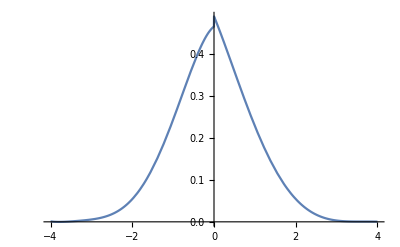

```mathematica
Plot[F5[x]/.{a->0.4658288313886247,b->0.0714779653473943,c->-0.2977093058582324,d->-0.18544799217655425,e->-0.04172617927391148,f->-0.0033181427219262875,g->0.4900476795018202,h->-0.2368247729065232,i->-0.08473363510159937,j->0.07555116734045479,k->-0.01662283568974064,l->0.001204640057180675},{x,-4,4}]
```

```mathematica
F51[x_]=F5[x]/.{a->0.4658288313886247,b->0.0714779653473943,c->-0.2977093058582324,d->-0.18544799217655425,e->-0.04172617927391148,f->-0.0033181427219262875,g->0.4900476795018202,h->-0.2368247729065232,i->-0.08473363510159937,j->0.07555116734045479,k->-0.01662283568974064,l->0.001204640057180675}
```

Piecewise[{{0.465829+0.071478 x-0.297709 x^2-0.185448 x^3-0.0417262 x^4-0.00331814 x^5, -∞<x<0}, {0.490048-0.236825 x-0.0847336 x^2+0.0755512 x^3-0.0166228 x^4+0.00120464 x^5, 0≤x<∞}, {0, True}}]

```mathematica
Solve[F51[x]==0,Reals]
```

{{x→-3.86792},{x→-3.69701},{x→4.18122},{x→4.6296}}

```mathematica
FindMinimum[F51[x],{x,-3.7}]
```

{-0.000150758,{x→-3.78758}}

```mathematica
F52[x_]=Piecewise[{{0.4658288313886247+0.0714779653473943 x-0.2977093058582324 x^2-0.18544799217655425 x^3-0.04172617927391148 x^4-0.0033181427219262875 x^5+0.00015075832338062867,-Infinity<x<0},{0.4900476795018202-0.2368247729065232 x-0.08473363510159937 x^2+0.07555116734045479 x^3-0.01662283568974064 x^4+0.001204640057180675 x^5,0≤x<Infinity}},0]
```

Piecewise[{{0.46598+0.071478 x-0.297709 x^2-0.185448 x^3-0.0417262 x^4-0.00331814 x^5, -∞<x<0}, {0.490048-0.236825 x-0.0847336 x^2+0.0755512 x^3-0.0166228 x^4+0.00120464 x^5, 0≤x<∞}, {0, True}}]

```mathematica
Integrate[F52[x],{x,-4,4}]
```

1.04053

```mathematica
f5[x_]=Piecewise[{{(0.4658288313886247+0.0714779653473943 x-0.2977093058582324 x^2-0.18544799217655425 x^3-0.04172617927391148 x^4-0.0033181427219262875 x^5+0.00015075832338062867)/1.040525418750527,-Infinity<x<0},{(0.4900476795018202-0.2368247729065232 x-0.08473363510159937 x^2+0.07555116734045479 x^3-0.01662283568974064 x^4+0.001204640057180675 x^5)/1.040525418750527,0≤x<Infinity}},0]
```

Piecewise[{{0.961053 (0.46598+0.071478 x-0.297709 x^2-0.185448 x^3-0.0417262 x^4-0.00331814 x^5), -∞<x<0}, {0.961053 (0.490048-0.236825 x-0.0847336 x^2+0.0755512 x^3-0.0166228 x^4+0.00120464 x^5), 0≤x<∞}, {0, True}}]

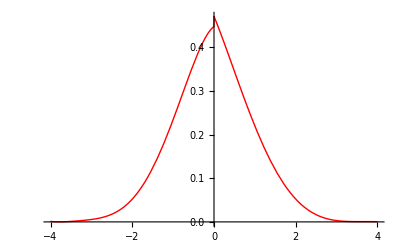

```mathematica
Plot[f5[x],{x,-4,4},PlotStyle->{Red,Thin}]
```

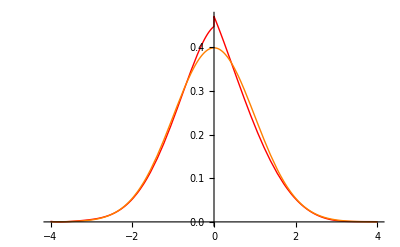

```mathematica
Plot[{f5[x],PDF[NormalDistribution[0,1],x]},{x,-4,4},PlotStyle->{{Red,Thin},{Orange,Thin}}]
```

```mathematica
(*Divergencia de Kullback-Leibler*)
```

```mathematica
N[Integrate[PDF[NormalDistribution[0,1],x],{x,-4,4}]]
```

0.999937

```mathematica
KL5 = N[Integrate[F[x]*Log[F[x]/f5[x]],{x,-4,4}]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-3.78331572120987}. NIntegrate obtained 0.00274814 and 2.38944×10^-7 for the integral and error estimates.

0.00274814

```mathematica
(*Verosimilitud*)
```

```mathematica
x5=Log[Table[f5[Extract[data,i]],{i,1,10000}]]
```

{-1.02215,-0.817313,-2.23363,-2.17822,-4.63228,-1.83101,-1.55578,-0.827895,-0.806427,-2.36152,-0.770625,-0.843474,-1.44814,-1.27778,9972,-1.16187,-1.04267,-1.62916,-0.922767,-1.58949,-1.30154,-0.89095,-1.61261,-0.7801,-1.59032,-1.62116,-0.957271,-1.46795,-0.947208}
 |  |  |  |

```mathematica
V5=Apply[Plus,x5]
```

-14167.4

```mathematica
(*BIC*)
```

```mathematica
BIC5 = -2*V5 + 12*Log[10000]
```

28445.3

### MOP DE GRADO 6

```mathematica
F6[x_] = Piecewise[{{a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6,-Infinity<x<0},{h+i*x+j*x^2+k*x^3+l*x^4+m*x^5+n*x^6,0≤x<Infinity}},0]
```

Piecewise[{{a+b x+c x^2+d x^3+e x^4+f x^5+g x^6, -∞<x<0}, {h+i x+j x^2+k x^3+l x^4+m x^5+n x^6, 0≤x<∞}, {0, True}}]

```mathematica
(*Momentos poblacionales*)
```

```mathematica
Integrate[x*F6[x],{x,-4,4}]
```

-8/105 (105 a-280 b+840 c-2688 d+8960 e-30720 f+107520 g-105 h-280 i-840 j-2688 k-8960 l-30720 m-107520 n)

```mathematica
Integrate[x^2*F6[x],{x,-4,4}]
```

64/315 (105 a-315 b+1008 c-3360 d+11520 e-40320 f+143360 g+105 h+315 i+1008 j+3360 k+11520 l+40320 m+143360 n)

```mathematica
Integrate[x^3*F6[x],{x,-4,4}]
```

-64/315 (315 a-1008 b+3360 c-11520 d+40320 e-143360 f+516096 g-315 h-1008 i-3360 j-11520 k-40320 l-143360 m-516096 n)

```mathematica
Integrate[x^4*F6[x],{x,-4,4}]
```

1/3465 1024 (693 a-2310 b+7920 c-27720 d+98560 e-354816 f+1290240 g+693 h+2310 i+7920 j+27720 k+98560 l+354816 m+1290240 n)

```mathematica
Integrate[x^5*F6[x],{x,-4,4}]
```

-1/3465 2048 (1155 a-3960 b+13860 c-49280 d+177408 e-645120 f+2365440 g-1155 h-3960 i-13860 j-49280 k-177408 l-645120 m-2365440 n)

```mathematica
Integrate[x^6*F6[x],{x,-4,4}]
```

1/45045 8192 (12870 a-45045 b+160160 c-576576 d+2096640 e-7687680 f+28385280 g+12870 h+45045 i+160160 j+576576 k+2096640 l+7687680 m+28385280 n)

```mathematica
Integrate[x^7*F6[x],{x,-4,4}]
```

-1/45045 8192 (45045 a-160160 b+576576 c-2096640 d+7687680 e-28385280 f+105431040 g-45045 h-160160 i-576576 j-2096640 k-7687680 l-28385280 m-105431040 n)

```mathematica
Integrate[x^8*F6[x],{x,-4,4}]
```

1/45045 262144 (5005 a-18018 b+65520 c-240240 d+887040 e-3294720 f+12300288 g+5005 h+18018 i+65520 j+240240 k+887040 l+3294720 m+12300288 n)

```mathematica
Integrate[x^9*F6[x],{x,-4,4}]
```

-(524288 (3003 a-10920 b+40040 c-147840 d+549120 e-2050048 f+7687680 g-3003 h-10920 i-40040 j-147840 k-549120 l-2050048 m-7687680 n))/15015

```mathematica
Integrate[x^10*F6[x],{x,-4,4}]
```

(4194304 (23205 a-85085 b+314160 c-1166880 d+4356352 e-16336320 f+61501440 g+23205 h+85085 i+314160 j+1166880 k+4356352 l+16336320 m+61501440 n))/255255

```mathematica
Integrate[x^11*F6[x],{x,-4,4}]
```

-(4194304 (23205 a-85680 b+318240 c-1188096 d+4455360 e-16773120 f+63365120 g-23205 h-85680 i-318240 j-1188096 k-4455360 l-16773120 m-63365120 n))/69615

```mathematica
Integrate[x^12*F6[x],{x,-4,4}]
```

1/1322685 67108864 (101745 a-377910 b+1410864 c-5290740 d+19918080 e-75246080 f+285143040 g+101745 h+377910 i+1410864 j+5290740 k+19918080 l+75246080 m+285143040 n)

```mathematica
Integrate[x^13*F6[x],{x,-4,4}]
```

-(134217728 (14535 a-54264 b+203490 c-766080 d+2894080 e-10967040 f+41674752 g-14535 h-54264 i-203490 j-766080 k-2894080 l-10967040 m-41674752 n))/101745

```mathematica
Integrate[x^14*F6[x],{x,-4,4}]
```

(268435456 (27132 a-101745 b+383040 c-1447040 d+5483520 e-20837376 f+79380480 g+27132 h+101745 i+383040 j+1447040 k+5483520 l+20837376 m+79380480 n))/101745

```mathematica
(*Solución del sistema*)
```

```mathematica
Solve[{Integrate[x*F6[x],{x,-4,4}]==(Apply[Plus,data])/(10^4),Integrate[x^2*F6[x],{x,-4,4}]==(Apply[Plus,data^2])/(10^4),Integrate[x^3*F6[x],{x,-4,4}]==(Apply[Plus,data^3])/(10^4),Integrate[x^4*F6[x],{x,-4,4}]==(Apply[Plus,data^4])/(10^4),Integrate[x^5*F6[x],{x,-4,4}]==(Apply[Plus,data^5])/(10^4),Integrate[x^6*F6[x],{x,-4,4}]==(Apply[Plus,data^6])/(10^4),Integrate[x^7*F6[x],{x,-4,4}]==(Apply[Plus,data^7])/(10^4),Integrate[x^8*F6[x],{x,-4,4}]==(Apply[Plus,data^8])/(10^4),Integrate[x^9*F6[x],{x,-4,4}]==(Apply[Plus,data^9])/(10^4),Integrate[x^10*F6[x],{x,-4,4}]==(Apply[Plus,data^10])/(10^4),Integrate[x^11*F6[x],{x,-4,4}]==(Apply[Plus,data^11])/(10^4),Integrate[x^12*F6[x],{x,-4,4}]==(Apply[Plus,data^12])/(10^4),Integrate[x^13*F6[x],{x,-4,4}]==(Apply[Plus,data^13])/(10^4),Integrate[x^14*F6[x],{x,-4,4}]==(Apply[Plus,data^14])/(10^4)},{a,b,c,d,e,f,g,h,i,j,k,l,m,n}]
```

{{a→0.288663,b→-0.629323,c→-1.28045,d→-0.843874,e→-0.270543,f→-0.0431455,g→-0.00274643,h→0.475303,i→-0.250505,j→-0.0015781,k→-0.0102739,l→0.0210331,m→-0.00641395,n→0.000584487}}

```mathematica
(*Obtención de la densidad y representación*)
```

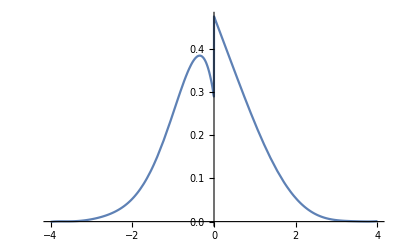

```mathematica
Plot[F6[x]/.{a->0.2886625524322359,b->-0.6293231494458125,c->-1.2804463902634062,d->-0.8438739321358711,e->-0.27054326750601676,f->-0.04314553984892315,g->-0.0027464270574617576,h->0.47530312808228375,i->-0.25050464099367414,j->-0.0015780957980581348,k->-0.010273877949629058,l->0.021033134275594414,m->-0.006413953381424689,n->0.0005844867257310953},{x,-4,4}]
```

```mathematica
F61[x_]=F6[x]/.{a->0.2886625524322359,b->-0.6293231494458125,c->-1.2804463902634062,d->-0.8438739321358711,e->-0.27054326750601676,f->-0.04314553984892315,g->-0.0027464270574617576,h->0.47530312808228375,i->-0.25050464099367414,j->-0.0015780957980581348,k->-0.010273877949629058,l->0.021033134275594414,m->-0.006413953381424689,n->0.0005844867257310953}
```

Piecewise[{{0.288663-0.629323 x-1.28045 x^2-0.843874 x^3-0.270543 x^4-0.0431455 x^5-0.00274643 x^6, -∞<x<0}, {0.475303-0.250505 x-0.0015781 x^2-0.0102739 x^3+0.0210331 x^4-0.00641395 x^5+0.000584487 x^6, 0≤x<∞}, {0, True}}]

```mathematica
Solve[F61[x]==0,Reals]
```

{{x→-3.94545}}

```mathematica
F61[-4]
```

-0.000664341

```mathematica
F62[x_]= Piecewise[{{0.2886625524322359-0.6293231494458125 x-1.2804463902634062 x^2-0.8438739321358711 x^3-0.27054326750601676 x^4-0.04314553984892315 x^5-0.0027464270574617576 x^6+0.0006643409096014352,-Infinity<x<0},{0.47530312808228375-0.25050464099367414 x-0.0015780957980581348 x^2-0.010273877949629058 x^3+0.021033134275594414 x^4-0.006413953381424689 x^5+0.0005844867257310953 x^6,0≤x<Infinity}},0]
```

Piecewise[{{0.289327-0.629323 x-1.28045 x^2-0.843874 x^3-0.270543 x^4-0.0431455 x^5-0.00274643 x^6, -∞<x<0}, {0.475303-0.250505 x-0.0015781 x^2-0.0102739 x^3+0.0210331 x^4-0.00641395 x^5+0.000584487 x^6, 0≤x<∞}, {0, True}}]

```mathematica
Integrate[F62[x],{x,-4,4}]
```

1.00519

```mathematica
f6[x_]=Piecewise[{{(0.2886625524322359-0.6293231494458125 x-1.2804463902634062 x^2-0.8438739321358711 x^3-0.27054326750601676 x^4-0.04314553984892315 x^5-0.0027464270574617576 x^6+0.0006643409096014352)/1.0051945574185988,-Infinity<x<0},{(0.47530312808228375-0.25050464099367414 x-0.0015780957980581348 x^2-0.010273877949629058 x^3+0.021033134275594414 x^4-0.006413953381424689 x^5+0.0005844867257310953 x^6)/1.0051945574185988,0≤x<Infinity}},0]
```

Piecewise[{{0.994832 (0.289327-0.629323 x-1.28045 x^2-0.843874 x^3-0.270543 x^4-0.0431455 x^5-0.00274643 x^6), -∞<x<0}, {0.994832 (0.475303-0.250505 x-0.0015781 x^2-0.0102739 x^3+0.0210331 x^4-0.00641395 x^5+0.000584487 x^6), 0≤x<∞}, {0, True}}]

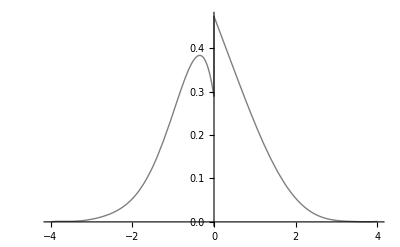

```mathematica
Plot[f6[x],{x,-4,4},PlotStyle->{Gray,Thin}]
```

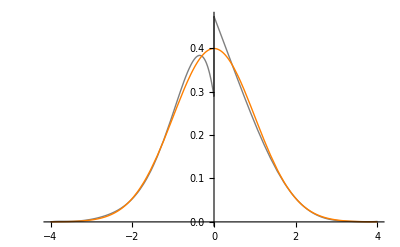

```mathematica
Plot[{f6[x],PDF[NormalDistribution[0,1],x]},{x,-4,4},PlotStyle->{{Gray,Thin},{Orange,Thin}}]
```

```mathematica
(*Divergencia de Kullback-Leibler*)
```

```mathematica
N[Integrate[PDF[NormalDistribution[0,1],x],{x,-4,4}]]
```

0.999937

```mathematica
F[x_]=(PDF[NormalDistribution[0,1],x])/0.9999366575163338
```

0.398968 ⅇ^(-x^2/2)

```mathematica
KL6 = N[Integrate[F[x]*Log[F[x]/f6[x]],{x,-4,4}]]
```

0.0032221

```mathematica
(*Verosimilitud*)
```

```mathematica
x6=Log[Table[f6[Extract[data,i]],{i,1,10000}]]
```

{-0.992536,-1.12094,-2.21968,-2.13058,-4.63408,-1.79108,-1.49481,-0.827435,-0.805506,-2.35235,-0.768011,-0.843143,-1.4188,-1.207,9972,-1.14831,-1.00526,-1.59202,-0.959578,-1.55388,-1.23048,-0.890188,-1.57609,-0.778065,-1.53177,-1.56486,-0.954464,-1.43766,-0.961497}
 |  |  |  |

```mathematica
V6=Apply[Plus,x6]
```

-14164.5

```mathematica
(*BIC*)
```

```mathematica
BIC6 = -2*V6 + 14*Log[10000]
```

28457.9

### EVOLUCIÓN DENSIDADES

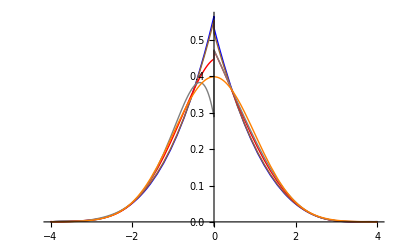

```mathematica
Plot[{f3[x],f4[x],f5[x],f6[x],PDF[NormalDistribution[0,1],x]},{x,-4,4},PlotStyle->{{Blue,Thin},{Brown,Thin},{Red,Thin},{Gray,Thin},{Orange,Thin}}]
```

### GRÁFICO DIVERGENCIAS

```mathematica
DKL = {{{3,0.011524576641722756}},{{4,0.009959305654295258}},{{5,0.0027481428121927925}},{{6,0.00322209710118929}}}
```

{{{3,0.0115246}},{{4,0.00995931}},{{5,0.00274814}},{{6,0.0032221}}}

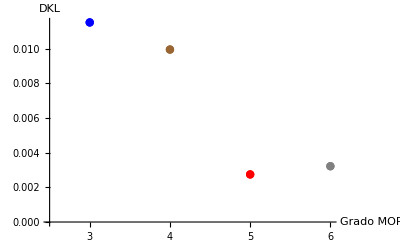

```mathematica
g1 =ListPlot[DKL,PlotStyle->{{Blue,Thin,PointSize[0.015]},{Brown,Thin,PointSize[0.015]},{Red,Thin,PointSize[0.015]},{Gray,Thin,PointSize[0.015]}},AxesLabel->{"Grado MOP","DKL"},AxesOrigin->{2.5,0},AxesStyle->Directive[Black, 12],PlotRange->Full,Ticks->{{3,4,5,6}, Automatic}]
```

```mathematica
DKL1 = {{3,0.011524576641722756},{4,0.009959305654295258},{5,0.0027481428121927925},{6,0.00322209710118929}}
```

{{3,0.0115246},{4,0.00995931},{5,0.00274814},{6,0.0032221}}

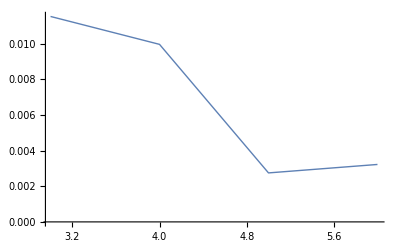

```mathematica
g2=ListLinePlot[DKL1,PlotStyle->Thin,PlotRange->Full]
```

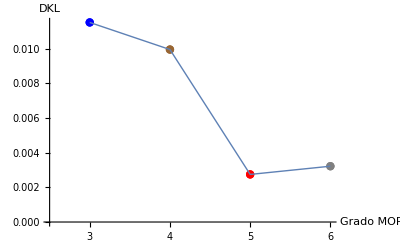

```mathematica
GDivergenciasNormalMDividiendo=Show[g1,g2]
```

### GRÁFICO VEROSIMILITUDES

```mathematica
V = {{{3,-14247.991664854904}},{{4,-14234.099152014558}},{{5,-14167.38743327167}},{{6,-14164.498094196431}}}
```

{{{3,-14248.}},{{4,-14234.1}},{{5,-14167.4}},{{6,-14164.5}}}

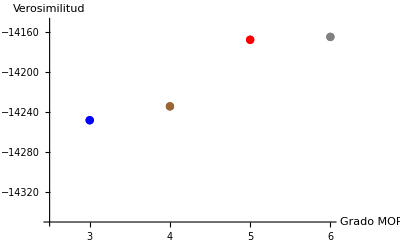

```mathematica
h1=ListPlot[V,PlotStyle->{{Blue,Thin,PointSize[0.015]},{Brown,Thin,PointSize[0.015]},{Red,Thin,PointSize[0.015]},{Gray,Thin,PointSize[0.015]}},AxesLabel->{"Grado MOP","Verosimilitud"},AxesOrigin->{2.5,-14350},AxesStyle->Directive[Black, 12],PlotRange->{-14350,-14150},Ticks->{{3,4,5,6},Automatic}]
```

```mathematica
V1 = {{3,-14247.991664854904},{4,-14234.099152014558},{5,-14167.38743327167},{6,-14164.498094196431}}
```

{{3,-14248.},{4,-14234.1},{5,-14167.4},{6,-14164.5}}

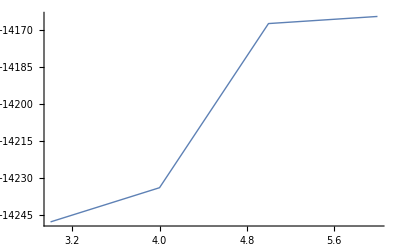

```mathematica
h2= ListLinePlot[V1,PlotStyle->Thin,PlotRange->Full]
```

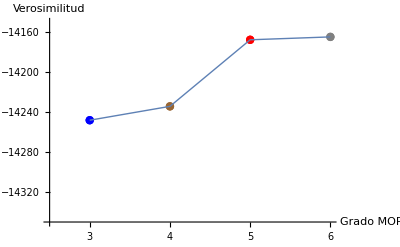

```mathematica
GrafVNDivMuestra1=Show[h1,h2]
```

```mathematica
(*Gráfico verosimilitudes con otra muestra*)
```

```mathematica
SeedRandom[4321]
```

```mathematica
data2 = RandomVariate[NormalDistribution[0,1],10^4]
```

{0.747051,-1.23297,0.881603,-0.0754897,-0.631166,0.511102,2.26024,-0.792594,0.443516,0.444986,0.765234,-1.37841,-0.376238,1.56308,9972,0.186956,-1.66499,0.78839,-1.00169,-0.262297,-0.431108,-0.292597,-0.477039,-0.627549,0.884375,0.424782,-0.0453317,-0.8449,0.982922}
 |  |  |  |

```mathematica
y3=Log[Table[f3[Extract[data2,i]],{i,1,10000}]]
```

{-1.31539,-1.82404,-1.45783,-0.633454,-1.14792,-1.08095,-3.53624,-1.3152,-1.01706,-1.01843,-1.33424,-2.01227,-0.90108,-2.30731,9972,-0.786265,-2.41991,-1.35843,-1.54638,-0.7969,-0.95255,-0.824259,-0.996313,-1.14428,-1.46083,-0.999587,-0.607873,-1.37143,-1.56977}
 |  |  |  |

```mathematica
y4=Log[Table[f4[Extract[data2,i]],{i,1,10000}]]
```

{-1.31205,-1.80708,-1.45036,-0.650641,-1.14631,-1.08585,-3.53038,-1.30887,-1.02452,-1.02584,-1.33032,-1.99271,-0.907648,-2.28751,9972,-0.804206,-2.39688,-1.35378,-1.53455,-0.807377,-0.957288,-0.833682,-0.999547,-1.14277,-1.45329,-1.00778,-0.626174,-1.36364,-1.5595}
 |  |  |  |

```mathematica
y5=Log[Table[f5[Extract[data2,i]],{i,1,10000}]]
```

{-1.26922,-1.72232,-1.3954,-0.818506,-1.1109,-1.07293,-3.49765,-1.24633,-1.02239,-1.02346,-1.28565,-1.91464,-0.941103,-2.21667,9972,-0.853271,-2.34814,-1.30686,-1.45281,-0.883924,-0.972905,-0.897926,-1.00157,-1.10811,-1.39811,-1.00882,-0.811603,-1.2947,-1.49757}
 |  |  |  |

```mathematica
y6=Log[Table[f6[Extract[data2,i]],{i,1,10000}]]
```

{-1.24942,-1.67383,-1.36871,-1.11417,-1.05547,-1.06445,-3.48147,-1.17648,-1.0166,-1.01762,-1.26492,-1.88109,-0.960503,-2.169,9972,-0.852945,-2.33857,-1.28494,-1.38567,-0.971969,-0.968693,-0.964669,-0.981263,-1.05323,-1.37129,-1.00371,-1.15941,-1.22369,-1.46589}
 |  |  |  |

```mathematica
L3 = Apply[Plus,y3]
```

-14307.2

```mathematica
L4 = Apply[Plus,y4]
```

-14290.2

```mathematica
L5 = Apply[Plus,y5]
```

-14214.1

```mathematica
L6 =  Apply[Plus,y6]
```

-14206.9

```mathematica
L = {{{3,-14307.20767081593}},{{4,-14290.218170569175}},{{5,-14214.124939912133}},{{6,-14206.899667611628}}}
```

{{{3,-14307.2}},{{4,-14290.2}},{{5,-14214.1}},{{6,-14206.9}}}

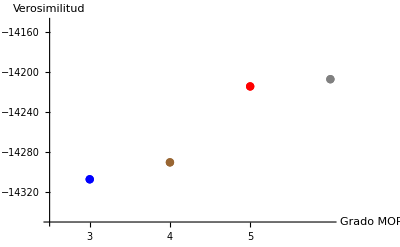

```mathematica
l1=ListPlot[L,PlotStyle->{{Blue,Thin,PointSize[0.015]},{Brown,Thin,PointSize[0.015]},{Red,Thin,PointSize[0.015]},{Gray,Thin,PointSize[0.015]}},AxesLabel->{"Grado MOP","Verosimilitud"},AxesOrigin->{2.5,-14350},AxesStyle->Directive[Black, 12],PlotRange->{-14350,-14150},Ticks->{{3,4,5}, Automatic}]
```

```mathematica
L1= {{3,-14307.20767081593},{4,-14290.218170569175},{5,-14214.124939912133},{6,-14206.899667611628}}
```

{{3,-14307.2},{4,-14290.2},{5,-14214.1},{6,-14206.9}}

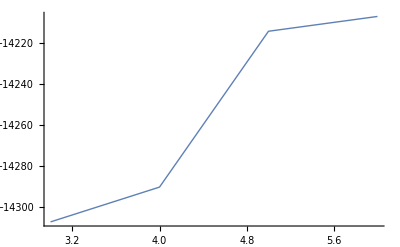

```mathematica
l2= ListLinePlot[L1,PlotStyle->Thin,PlotRange->Full]
```

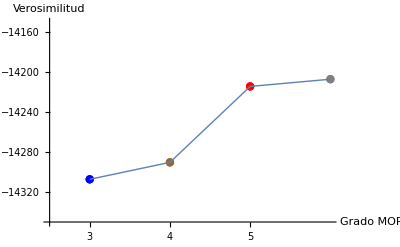

```mathematica
GrafVNDivMuestra2=Show[l1,l2]
```

```mathematica
(*Comparación verosimilitudes ambas muestras*)
```

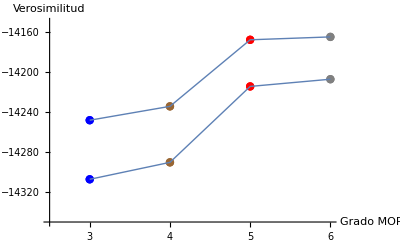

```mathematica
Show[GrafVNDivMuestra1,GrafVNDivMuestra2]
```

### MOMENTOS

```mathematica
f3estimada = Table[Integrate[x^i*f3[x],{x,-4,4}],{i,1,16}]
```

{-0.0226569,0.906482,-0.090641,2.80527,-0.743455,14.7515,-7.42077,108.845,-80.2718,1015.17,-907.447,11079.,-10546.1,133774.,-124783.,1.72238×10^6}

```mathematica
f4estimada = Table[Integrate[x^i*f4[x],{x,-4,4}],{i,1,16}]
```

{-0.0261559,0.92454,-0.117698,2.91779,-1.02976,15.8589,-10.841,121.857,-124.095,1177.1,-1494.65,13138.3,-18657.1,160234.,-239269.,2.06436×10^6}

```mathematica
f5estimada = Table[Integrate[x^i*f5[x],{x,-4,4}],{i,1,16}]
```

{-0.0200559,0.956809,-0.0637003,2.88929,-0.440968,14.5403,-3.68935,101.16,-31.7212,882.416,-267.278,9037.78,-2121.6,103665.,-14712.8,1.28748×10^6}

```mathematica
f6estimada = Table[Integrate[x^i*f6[x],{x,-4,4}],{i,1,16}]
```

{-0.0248193,1.00144,-0.0983036,3.09666,-0.801034,16.2625,-7.94856,119.803,-85.6455,1111.1,-980.307,12033.2,-11760.8,144372.,-146124.,1.85284×10^6}

```mathematica
Table[{Integrate[x^i*f3[x],{x,-4,4}],Integrate[x^i*f4[x],{x,-4,4}],Integrate[x^i*f5[x],{x,-4,4}],Integrate[x^i*f6[x],{x,-4,4}]},{i,1,16}]
```

{{-0.0226569,-0.0261559,-0.0200559,-0.0248193},{0.906482,0.92454,0.956809,1.00144},{-0.090641,-0.117698,-0.0637003,-0.0983036},{2.80527,2.91779,2.88929,3.09666},{-0.743455,-1.02976,-0.440968,-0.801034},{14.7515,15.8589,14.5403,16.2625},{-7.42077,-10.841,-3.68935,-7.94856},{108.845,121.857,101.16,119.803},{-80.2718,-124.095,-31.7212,-85.6455},{1015.17,1177.1,882.416,1111.1},{-907.447,-1494.65,-267.278,-980.307},{11079.,13138.3,9037.78,12033.2},{-10546.1,-18657.1,-2121.6,-11760.8},{133774.,160234.,103665.,144372.},{-124783.,-239269.,-14712.8,-146124.},{1.72238×10^6,2.06436×10^6,1.28748×10^6,1.85284×10^6}}

### GRÁFICO BIC

```mathematica
B = {{{3,28569.666052685618}},{{4,28560.301707748877}},{{5,28445.298951007055}},{{6,28457.94095360053}}}
```

{{{3,28569.7}},{{4,28560.3}},{{5,28445.3}},{{6,28457.9}}}

```mathematica
B1 = {{3,28569.666052685618},{4,28560.301707748877},{5,28445.298951007055},{6,28457.94095360053}}
```

{{3,28569.7},{4,28560.3},{5,28445.3},{6,28457.9}}

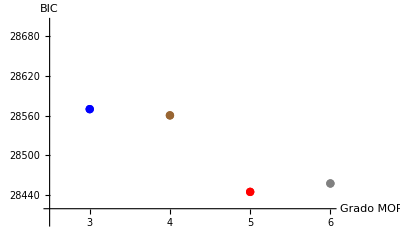

```mathematica
b1=ListPlot[B,PlotStyle->{{Blue,Thin,PointSize[0.015]},{Brown,Thin,PointSize[0.015]},{Red,Thin,PointSize[0.015]},{Gray,Thin,PointSize[0.015]}},AxesLabel->{"Grado MOP","BIC"},AxesOrigin->{2.5,28420},AxesStyle->Directive[Black, 12],PlotRange->{28400,28700},Ticks->{{3,4,5,6}, Automatic}]
```

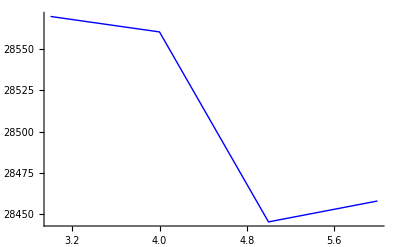

```mathematica
b2= ListLinePlot[B1,PlotStyle->{Blue,Thin},PlotRange->Full]
```

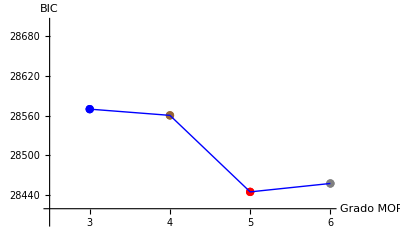

```mathematica
GrafBICNormalMuestra1MD = Show[b1,b2]
```

```mathematica
(*Gráfico BIC con otra muestra*)
```

```mathematica
SeedRandom[4321]
```

```mathematica
BIC3N = -2L3 +  + 8*Log[10000]
```

28688.1

```mathematica
BIC4N = -2L4 +  + 10*Log[10000]
```

28672.5

```mathematica
BIC5N = -2L5 +  + 12*Log[10000]
```

28538.8

```mathematica
BIC6N = -2L6 +  + 14*Log[10000]
```

28542.7

```mathematica
BN = {{{3,28688.098064607668}},{{4,28672.53974485811}},{{5,28538.773964287982}},{{6,28542.744100430922}}}
```

{{{3,28688.1}},{{4,28672.5}},{{5,28538.8}},{{6,28542.7}}}

```mathematica
BN1= {{3,28688.098064607668},{4,28672.53974485811},{5,28538.773964287982},{6,28542.744100430922}}
```

{{3,28688.1},{4,28672.5},{5,28538.8},{6,28542.7}}

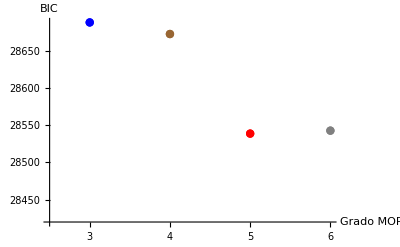

```mathematica
bN1=ListPlot[BN,PlotStyle->{{Blue,Thin,PointSize[0.015]},{Brown,Thin,PointSize[0.015]},{Red,Thin,PointSize[0.015]},{Gray,Thin,PointSize[0.015]}},AxesLabel->{"Grado MOP","BIC"},AxesOrigin->{2.5,28420},AxesStyle->Directive[Black, 12],PlotRange->Full,Ticks->{{3,4,5,6}, Automatic}]
```

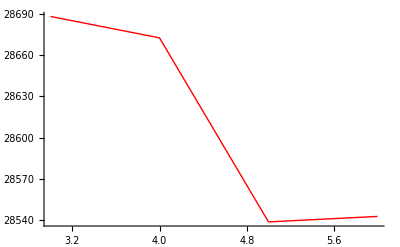

```mathematica
bN2= ListLinePlot[BN1,PlotStyle->{Red,Thin},PlotRange->Full]
```

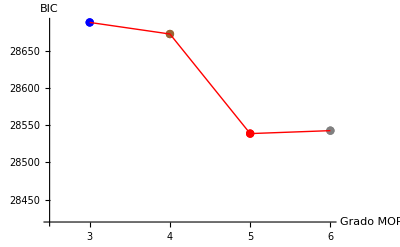

```mathematica
GrafBICNormalMuestra2MD = Show[bN1,bN2]
```

```mathematica
(*Comparación gráficos BIC ambas muestras*)
```

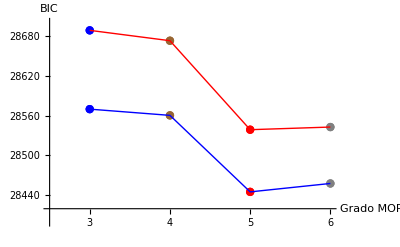

```mathematica
Show[GrafBICNormalMuestra1MD,GrafBICNormalMuestra2MD]
```